```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY187/sec_int_data/862nm.dat"]
```

{{1.45287,-0.197744},{1.39708,-0.618114},{1.35876,-0.929984},{1.32403,-1.3309},{1.28662,-1.83258},{1.25869,-2.28937},{1.22636,-2.70196},{1.19613,-2.77817},{1.17366,-3.85215},{1.15413,-inf},{1.12528,-inf},{1.11495,-inf},{1.10625,-8.20963},{1.09912,-3.42194},{1.09306,-2.2367},{1.0888,-1.79108},{1.08648,-2.19212},{1.08572,-2.8067},{1.08632,-inf},{1.0888,-inf},{1.09505,-3.01005},{1.09559,-2.2677},{1.12528,-1.30952},{1.14263,-0.801067},{1.16354,-0.568808},{1.19414,-0.377213},{1.22405,-0.294237},{1.25343,-0.236976},{1.28081,-0.226938},{1.31748,-0.194447},{1.36987,-0.180707},{1.42194,-0.177298},{1.47153,-0.164851},{1.11308,-1.21652}}

0.171499 (-43.9548+7.79295 -inf)+0.141292 (35.8573-6.96877 -inf) x

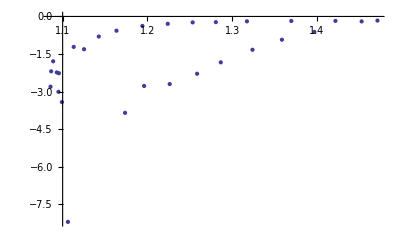

-Graphics-

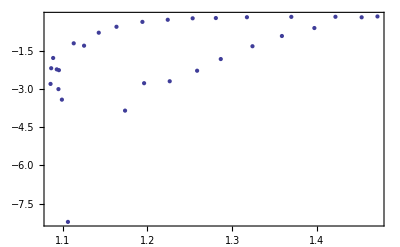

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```